## Solving coupled ODEs for Friedmann equation and scalar inflaton field equation

Generally:

H^2 = (8πG)/3(1/2(ϕ̇)^2 + V(ϕ))

ϕ^(..) + 3H ϕ̇ + V'(ϕ) = 0

From Wiltshire’s Intro to quantum cosmology  (equations 3.54 & 3.56)

-((ȧ)/a)^2+ (ϕ̇)^2 + V(ϕ)= 0
ϕ^(..) + 3H ϕ̇ + 1/2 V'(ϕ) = 0

Dots: derivative with respect to time  
Prime: derivative with respect to scalar field ϕ
k = 0 (flat universe)

H = (ȧ)/a
Ḣ = -(ϕ̇)^2/2 
M_PL^2 = 1/(8πG) = 1

## Scalar potentials

Following selected potentials presented in Planck X paper, and simplifying: https://arxiv.org/pdf/1807.06211.pdf
Use initial conditions found via Dr. McGuigan’s code for Wiltshire functions
 Find that for t = 0.001; a = 0.114471, ϕ = -1.6743, ϕ̇ = 333.333

## Case Type 1: Constant potential

#### Case #1: V(ϕ) = Constant

V = 1

```mathematica
ClearAll["Global`*"]
```

```mathematica
ode1= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+a[t]^2==0};
```

```mathematica
ode2 =  {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] ==0};
```

```mathematica
sol = NDSolve[{ode1,ode2,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

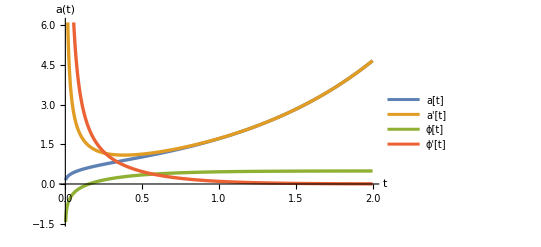

```mathematica
Plot[Evaluate[{a[t], a'[t], ϕ[t],ϕ'[t]}/.sol],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

Parametric Plot ϕ(t) vs a(t)

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

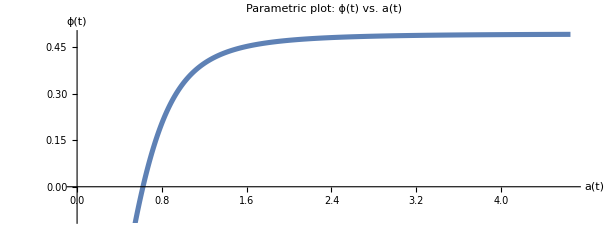

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)"  ]
```

#### Parametric Plot α̇(t) vs ϕ̇(t) (following Wiltshire)

InterpolatingFunction::dmval: Input value {0.002003} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

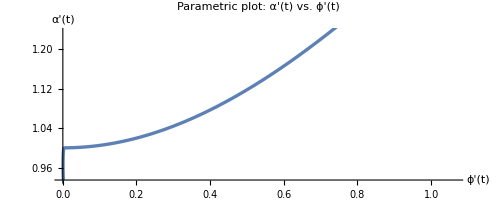

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol],{t,0.002,3}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]} , PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)" ]
```

NOTE: Looks somewhat like Wiltshire’s figure. My guess is we have only solved for the positive solution of sqrt, and Wiltshire also plots time reversal solutions which I did not. There is also a critical point at (0,1)

## Case Type 2: Inflationary Model - Power-law potentials

## Case #2: V(ϕ)= λM_Pl^(10/3)ϕ^(2/3) *couldn’t solve*

V = ϕ^(2/3)

```mathematica
ode3 = {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(ϕ[t])^(2/3)==0};
```

```mathematica
ode4 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +(1/3)(ϕ[t])^(-1/3)==0};
```

```mathematica
sol2 = NDSolve[{ode3,ode4,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::mxst: Maximum number of 239235 steps reached at the point t == 0.00673938.

NDSolve::mxst: Maximum number of 239235 steps reached at the point t == 0.002.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[{{0.005, 0.00673938}}, <>],ϕ→InterpolatingFunction[{{0.005, 0.00673938}}, <>]}}

```mathematica
Plot[Evaluate[{a[t],ϕ[t]}/.sol2],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","ϕ[t]"} ]
```

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol2],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]} ]
```

## Case #3: V(ϕ)= λM_Pl^3ϕ

V = ϕ

```mathematica
ode5= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(ϕ[t])==0};
```

```mathematica
ode6 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +0.5==0};
```

```mathematica
sol3 = NDSolve[{ode5,ode6,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200501} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

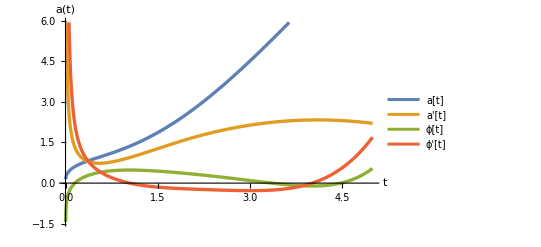

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol3],{t,.002,5}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

a(t) starts to decrease as t → ∞
Potential well

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

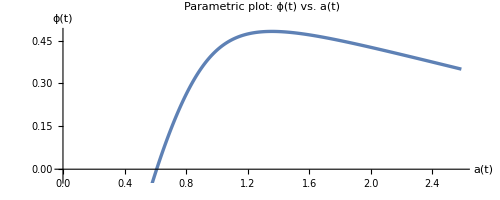

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol3],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)"  ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

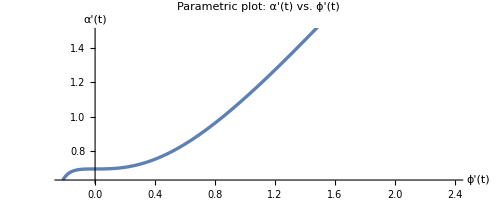

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol3],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"  ]
```

```mathematica
Plot3D[{(a)^2(ϕ)},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

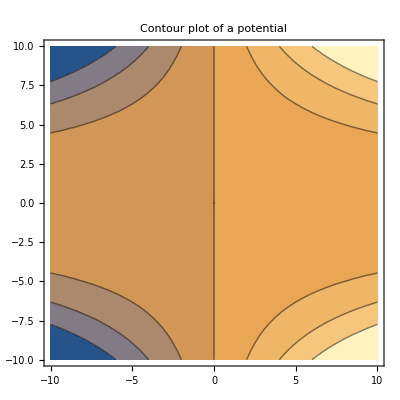

```mathematica
ContourPlot[{(a)^2(ϕ)},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "Contour plot of a potential"]
```

## Case #4: V(ϕ)= λM_Pl^2ϕ^2

V = ϕ^2

```mathematica
ode7= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(ϕ[t])^2==0};
```

```mathematica
ode8 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +ϕ[t]==0};
```

```mathematica
sol4 = NDSolve[{ode7,ode8,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200501} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

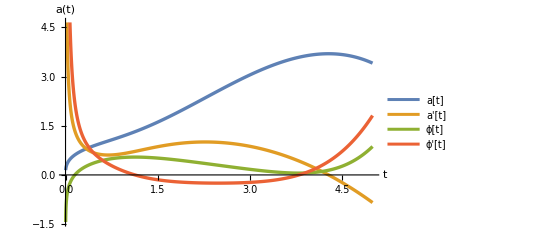

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol4],{t,.002,5}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"}]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

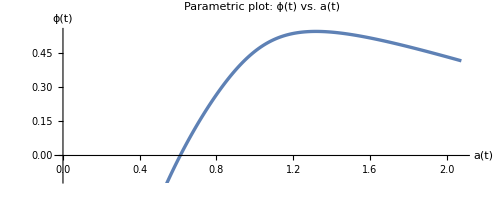

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol4],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol3],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

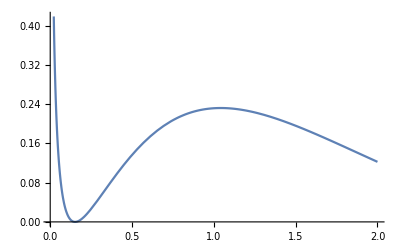

```mathematica
Plot[Evaluate[{(ϕ[t])^2}/.sol3],{t,.002,2}]
```

```mathematica
Plot3D[{(a)^2(ϕ)^2},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

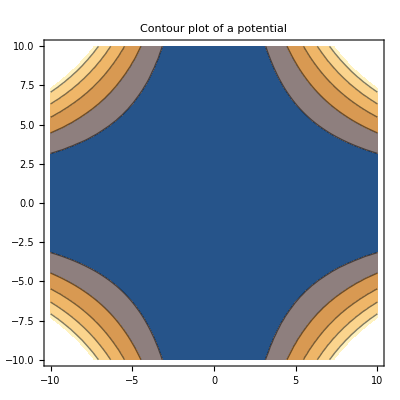

```mathematica
ContourPlot[{(a)^2(ϕ)^2},{ϕ, -10, 10},{a,-10,10},  PlotLabel-> "Contour plot of a potential"]
```

## Case #5: V(ϕ)= λM_Pl^(8/3)ϕ^(4/3) *couldn’t solve*

V = ϕ^(4/3)

```mathematica
ode9= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(ϕ[t])^(4/3)==0};
```

```mathematica
ode10 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] + 2/3(ϕ[t])^(1/3)==0};
```

```mathematica
sol5 = NDSolve[{ode9,ode10,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol5],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

## Case #6: V(ϕ)= λM_Plϕ^3

V = ϕ^3

```mathematica
ode11= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(ϕ[t])^3==0};
```

```mathematica
ode12 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +1.5(ϕ[t])^2==0};
```

```mathematica
sol6 = NDSolve[{ode11,ode12,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00200001, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00201002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

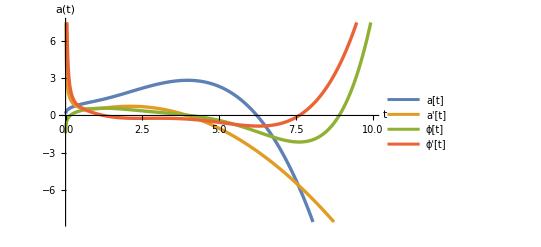

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol6],{t,.002,10}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

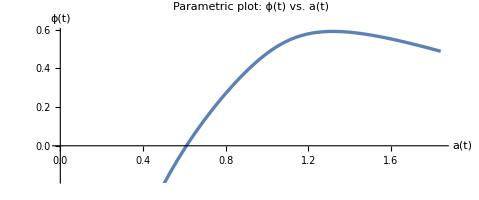

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol6],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

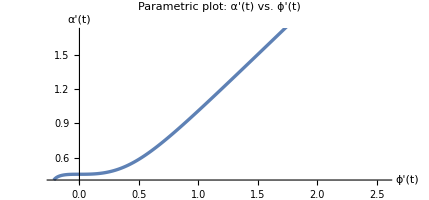

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol6],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

```mathematica
Plot3D[{(a)^2(ϕ)^3},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

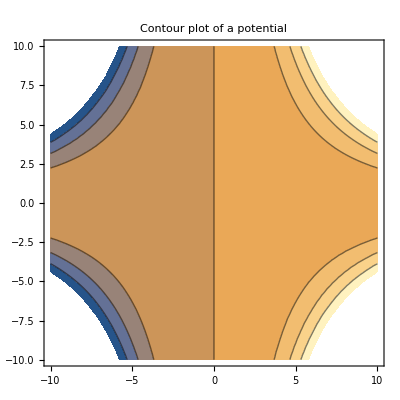

```mathematica
ContourPlot[{(a)^2(ϕ)^3},{ϕ, -10, 10},{a,-10,10},  PlotLabel-> "Contour plot of a potential"]
```

## Case #7: V(ϕ)= λϕ^4

V = ϕ^4

```mathematica
ode13= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(ϕ[t])^4==0};
```

```mathematica
ode14 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +2(ϕ[t])^3==0};
```

```mathematica
sol7 = NDSolve[{ode13,ode14,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199998, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200501} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

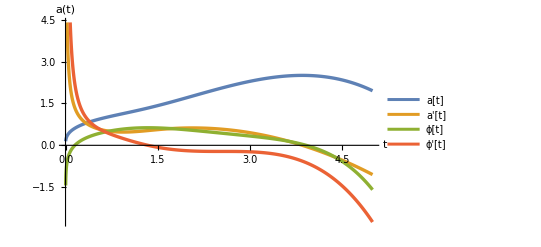

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol7],{t,.002,5}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

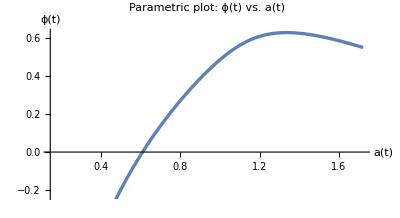

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol7],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

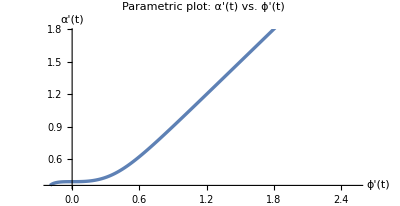

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol7],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

```mathematica
Plot3D[{(a)^2(ϕ)^4},{ϕ, -10, 10},{a,-10,100}, PlotLabel-> "3D plot of a potential"]
```

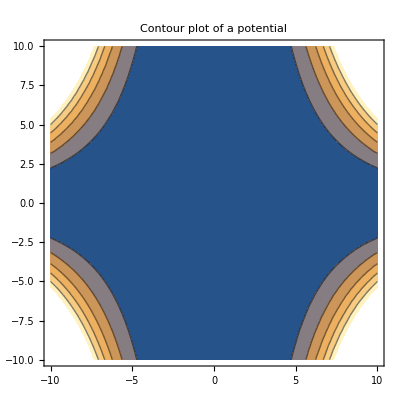

```mathematica
ContourPlot[{(a)^2(ϕ)^4},{ϕ, -10, 10},{a,-10,10},  PlotLabel-> "Contour plot of a potential"]
```

## Case Type 3: Inflationary Model - Non-minimal coupling

#### Case #8: λ^4 ϕ^4 + ξϕ^2 R/2

V =  ϕ^2 + ϕ^4   (simplified)

```mathematica
ode15= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2((ϕ[t])^4+(ϕ[t])^2 )==0};
```

```mathematica
ode16 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +ϕ[t]+2(ϕ[t])^3==0};
```

```mathematica
sol8= NDSolve[{ode15,ode16,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199998, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200501} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

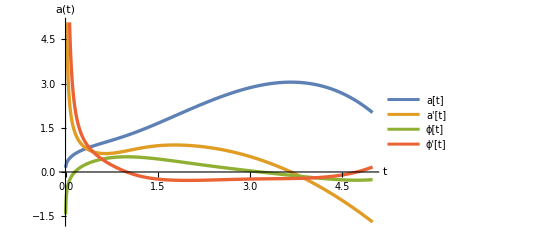

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol8],{t,.002,5}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

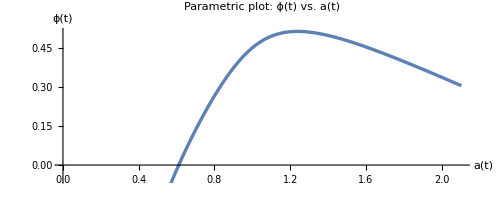

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol8],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

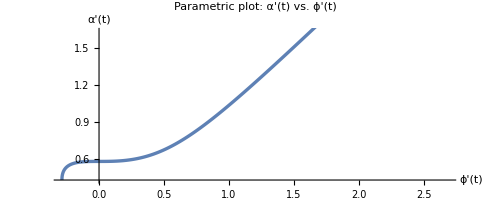

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol8],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

```mathematica
Plot3D[{(a)^2((ϕ)^2 + (ϕ)^4)},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

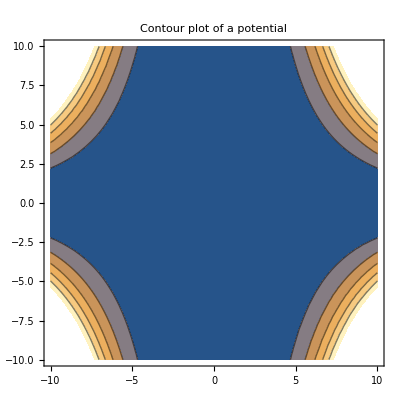

```mathematica
ContourPlot[{(a)^2((ϕ)^2 + (ϕ)^4)},{ϕ, -10, 10},{a,-10,10},  PlotLabel-> "Contour plot of a potential"]
```

## Case Type 4: Inflationary model - Natural inflation

### Case #9: V(ϕ) = Λ^4[1-cos(ϕ)]

V= 1 - cos(ϕ)

```mathematica
ode17= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2 (1 -Cos[ϕ[t]])==0};
```

```mathematica
ode18 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] - Sin[ϕ[t]]==0};
```

```mathematica
sol9 = NDSolve[{ode17,ode18,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200401} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

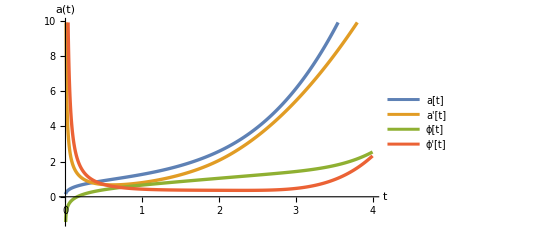

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol9],{t,.002,4}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

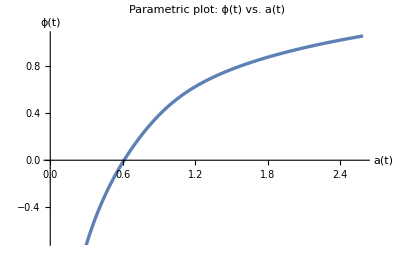

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol9],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

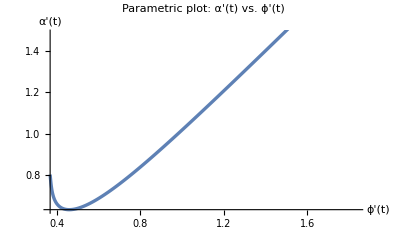

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol9],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

```mathematica
Plot3D[{(a)^2(1 - Cos[ϕ])},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

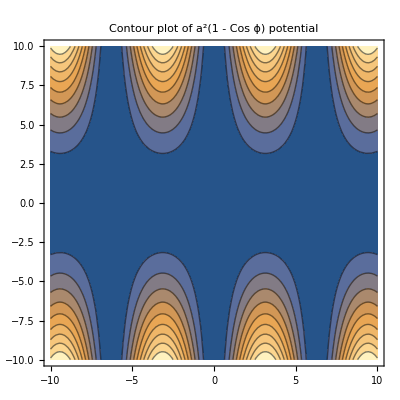

```mathematica
ContourPlot[{(a)^2(1 - Cos[ϕ])},{ϕ, -10, 10},{a,-10,10},  PlotLabel-> "Contour plot of a^2(1 - Cos ϕ) potential"]
```

## Case Type 5: Inflationary Model - Hilltop quadratic

#### Case #10: V(ϕ) = Λ^4(1- ϕ^2/μ_2^2+ ...)

Using simplified form and only expanding to ϕ^4
V = 1 - ϕ^2 + ϕ^3-ϕ^4

```mathematica
ode19= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(1-(ϕ[t])^2+(ϕ[t])^3-(ϕ[t])^4)==0};
```

```mathematica
ode20= {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] -ϕ[t]+1.5(ϕ[t])^2-2(ϕ[t])^3==0};
```

```mathematica
sol10 = NDSolve[{ode19,ode20,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00200003, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200501} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

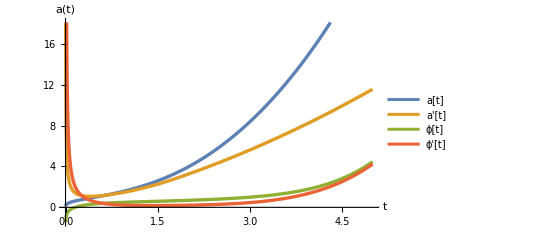

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol10],{t,.002,5}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

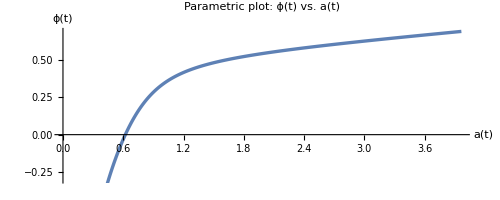

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol10],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

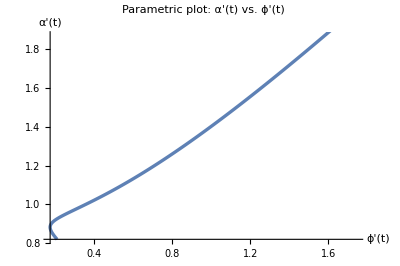

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol10],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

```mathematica
Plot3D[{(a)^2(1 -(ϕ)^2+(ϕ)^3-(ϕ)^4)},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

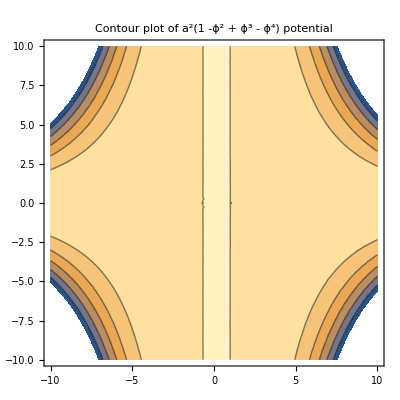

```mathematica
ContourPlot[{(a)^2(1 -(ϕ)^2+(ϕ)^3-(ϕ)^4)},{ϕ, -10, 10},{a,-10,10},  PlotLabel-> "Contour plot of a^2(1 -ϕ^2 + ϕ^3 - ϕ^4) potential"]
```

## Case Type 6 : Inflationary Model - Potential with exponential tails

#### Case #11: V(ϕ) = Λ^4[1- exp[-qϕ/M_Pl]+ ...]

V = 1 - e^-ϕ

```mathematica
ode21= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2 (1 -Exp[-ϕ[t]])==0};
```

```mathematica
ode22= {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +0.5(Exp[-ϕ[t]])==0};
```

```mathematica
sol11 = NDSolve[{ode21,ode22,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00200001, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00200701} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

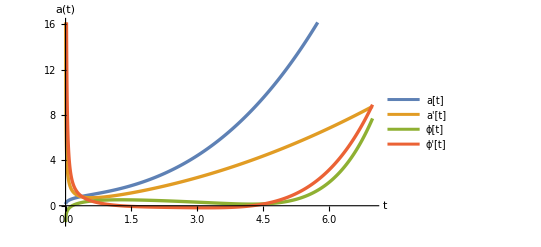

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol11],{t,.002,7}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

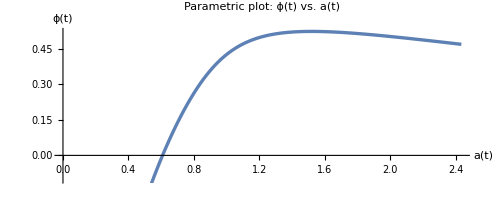

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol11],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

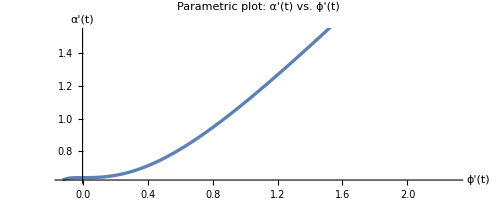

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol11],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

```mathematica
Plot3D[{(a)^2(1 - Exp[-ϕ])},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D plot of a potential"]
```

-Graphics3D-

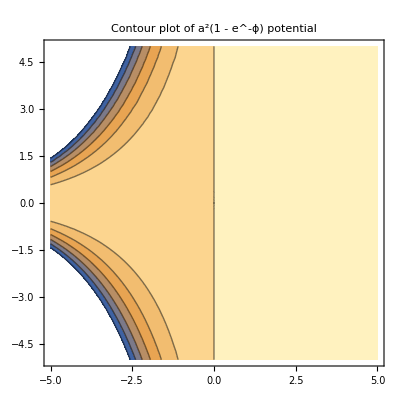

```mathematica
ContourPlot[{(a)^2(1 - Exp[-ϕ])},{ϕ, -5, 5},{a,-5,5},  PlotLabel-> "Contour plot of a^2(1 - e^-ϕ) potential"]
```

## Case Type 7 : Inflationary Model - Spontaneously broken SUSY *couldn’t solve*

Case #12: V(ϕ) = Λ^4(1+ α_h log(ϕ/M_Pl+ ...)

V = 1+log(ϕ)

```mathematica
ode23= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2 (1 +Log[ϕ[t]])==0};
```

```mathematica
ode24= {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] +0.5(1/(ϕ[t]))==0};
```

```mathematica
sol12 = NDSolve[{ode23,ode24,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.002, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

NDSolve::mxst: Maximum number of 239237 steps reached at the point t == 0.00547747.

{{a→InterpolatingFunction[{{0.005, 0.00547747}}, <>],ϕ→InterpolatingFunction[{{0.005, 0.00547747}}, <>]}}

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol12],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends->{"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"} ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol12],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol11],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

## Case Type 8: Inflationary Model - R + R^2/(6 M^2) (Starobinsky)

#### Case #13: V(ϕ) = (1 - (exp[-√(2/3) ϕ/M_Pl]))^2

V = (1 - (exp[-√(2/3) ϕ]))^2

```mathematica
ode25= {-(a'[t])^2+((a[t])^2(ϕ'[t])^2)+(a[t])^2(1-Exp[-Sqrt[2/3]ϕ[t]])^2==0};
```

```mathematica
ode26 = {ϕ''[t]+(3a'[t] ϕ'[t])/a[t] + √(2/3) ⅇ^(-√(2/3) ϕ[t]) (1-ⅇ^(-√(2/3) ϕ[t]))==0};
```

```mathematica
sol13 = NDSolve[{ode25,ode26,a[0.001]==.114471, ϕ[.001] == -1.6743, ϕ'[.001] == 333.333}, {a,ϕ}, {t,0.005,2}]
```

NDSolve::ndsz: At t == 0.00199998, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00100701} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

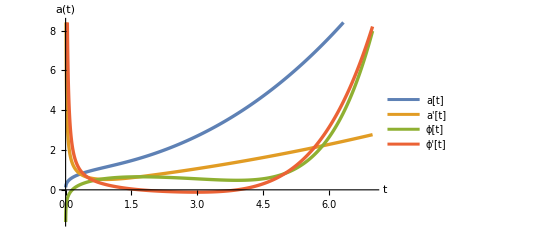

```mathematica
Plot[Evaluate[{a[t],a'[t],ϕ[t], ϕ'[t]}/.sol13],{t,.001,7}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLegends-> {"a[t]","a'[t]","ϕ[t]", "ϕ'[t]"}  ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

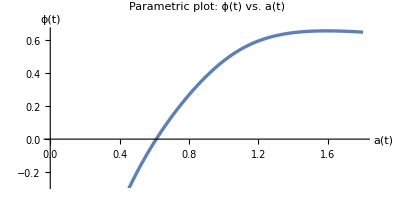

```mathematica
ParametricPlot[Evaluate[{ a[t],  ϕ[t]}/.sol13],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: ϕ(t) vs. a(t)" ]
```

InterpolatingFunction::dmval: Input value {0.002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

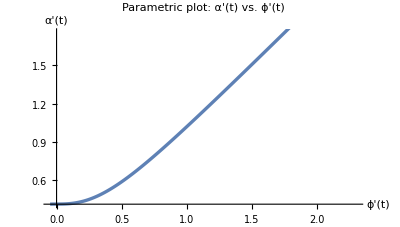

```mathematica
ParametricPlot[Evaluate[{ ϕ'[t],a'[t]/a[t]  }/.sol13],{t,.002,2}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"ϕ'(t)","α'(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.006]}, PlotLabel-> "Parametric plot: α'(t) vs. ϕ'(t)"]
```

InterpolatingFunction::dmval: Input value {0.00230639} lies outside the range of data in the interpolating function. Extrapolation will be used.

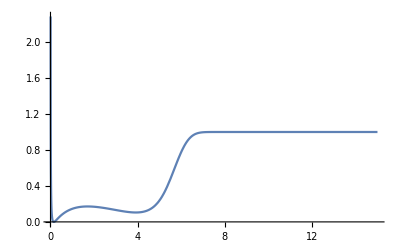

```mathematica
Plot[Evaluate[{(1-Exp[-Sqrt[2/3]ϕ[t]])^2}/.sol13],{t,.002,15}]
```

```mathematica
Plot3D[{(a)^2(1-Exp[-Sqrt[2/3]ϕ])^2}, {ϕ, -1, 10}, {a, -1,10}, PlotLabel-> "3D plot of a^2 potential"]
```

-Graphics3D-

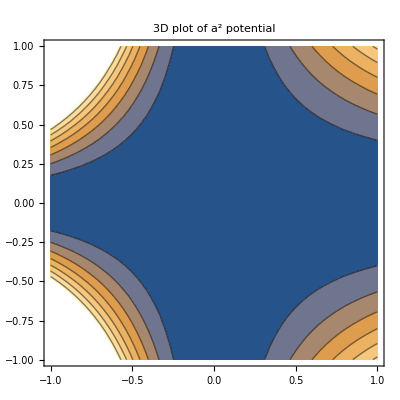

```mathematica
ContourPlot[{(a)^2(1-Exp[-Sqrt[2/3]ϕ])^2}, {ϕ, -1, 1}, {a, -1,1}, PlotLabel-> "3D plot of a^2 potential"]
```